## Recording the drums

```mathematica
Hmm=AudioCapture[]
```

```mathematica
Spectrogram[Hmm,FrameLabel->{"sec","Hz"}]
```

-Graphics-

```mathematica
Spectrogram[Hmm,FrameLabel->{"sec","Hz"},PlotRange->{All,{0,800}}]
```

-Graphics-

```mathematica
PArray=PeriodogramArray[Hmm];
{p1,p2,p3}={2925,4990,5040};
ListPlot[PArray,
PlotRange->{{2500,5500},All},
Joined->True,
GridLines->{{p1,p2,p3},Automatic}]
```

-Graphics-

```mathematica
Dimensions[PArray]
```

{463050}

```mathematica
?NDEigenvalues
```

```mathematica
?Disk
```

```mathematica
{
{λ1,λ2,λ3,λ4,λ5,λ6},
{v1,v2,v3,v4,v5,v6}
}=NDEigensystem[{-Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,True]},u[x,y],{x,y}∈Disk[],6]
```

{{5.78323,14.6827,14.6827,26.3784,26.3791,30.4787},{InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y],InterpolatingFunction[…][x,y]}}

```mathematica
{λ1,λ2,λ3,λ4,λ5,λ6}/λ1
```

{1.,2.53884,2.53884,4.56119,4.56131,5.2702}

```mathematica
TabView[Map[Plot3D[#,{x,y}∈Disk[]]&,{v1,v2,v3,v4,v5,v6}]]
```

123456

```mathematica
N[p2/p1]
λ4/λ3
```

1.70598

1.79657

64.4281/(1+0.00580356 (-131.891+x)^2)

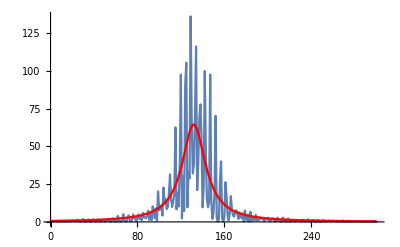

```mathematica
Gabba=PArray⟦2800;;3100⟧;
f[x_]=Normal[NonlinearModelFit[Gabba,a/(1+b (x-c)^2),{a,b,c},x]]
Show[
ListPlot[Gabba,
PlotRange->All,
Joined->True],
Plot[f[x],{x, 0,300},
PlotStyle->Red,PlotRange->All]
]
```

```mathematica
{fmin,fmax}={1,800};
n=100;
Spectrogram[Hmm,FrameLabel->{"sec","Hz"},
Method->{"MelFrequency",n,fmin,fmax}]
```

-Graphics-

```mathematica
Options[Spectrogram]
```

{AlignmentPoint→Center,AspectRatio→1/3,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ColorRules→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DataRange→Automatic,DataReversed→False,DisplayFunction:>$DisplayFunction,Epilog→{},FormatType:>TraditionalForm,Frame→Automatic,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},MaxPlotPoints→Automatic,Mesh→False,MeshStyle→GrayLevel[-1+GoldenRatio],Method→Automatic,PixelConstrained→False,PlotLabel→None,PlotLegends→None,PlotRange→Automatic,PlotRangeClipping→Automatic,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,SampleRate→Automatic,Ticks→Automatic,TicksStyle→{}}

```mathematica
ListPlot[AudioData[Hmm],
PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[AudioData[Hmm]
```